## investigating RF

RF is made from three things:

We track the vector of crossover events involving chromatids {13,14,23,24} where out of n crossovers, n-k start at chromatid 1, i of which end at 3 (n-k-i end at 4). Otherwise, k start at chromatid 2, j of which end at 3 (k-j end at 4).

Here we assume sisters are never involved in the crossovers (i.e., when the DSBs are formed and strand invasion occurs, it isn’t to the sister)

Just to clarify, let p equal the chance that the second of the sister chromatids is involved in a given crossover event (we’ll set p=1/2 next, but it can be hard to know where the factors of 2 come from).

## modelling RF

we define the following two values :

match state is a vector , where  if the markers on the th chromatid are “matched” (non-recombinant), and  otherwise (recombinant).

event count is a vector , where  is the number of crossover events the th chromatid has gone through.

both of these are required to model RF, and neither can be derived from the other .

additionally, let  be the proportion of chromatids in the tetrad that are unmatched (visibly recombinant) .

### match state cannot be derived from event count

our chromatids start out like so:

```mathematica
1 .------
2 .------
3 .xxxxxx
4 .xxxxxx
```

where . indicates the centromere. now consider the CO sequence [13, 23]:

first crossover: 13:

```mathematica
1 .---|xxx
2 .------
3 .xxx|---
4 .xxxxxx
```

second crossover: 23:

```mathematica
1 .---|xxx
2 .----|--
3 .xxx|-|--
4 .xxxxxx
```

chromatid 1: 1 CO, looks recombinant (“unmatched”)

chromatid 2: 1 CO, looks nonrecombinant (“matched”)

chromatid 3: 2 COs, looks recombinant (“unmatched”)

so magnitude or parity of the event count can’t be used to determine the match state, since the same event count magnitude/parity can be found on both matched and unmatched chromatids. 
additionally, match state is required to model RF since it tells us which chromatids are visibly recombinant.

### event count cannot be derived from match state

as seen above, a single match state can correspond to multiple different event counts. so event count can’t be derived from match state, either.
additionally, we need event count to be able to weight the chromatids for drive (since we assume the actual occurrences of COs are what cause drive, not whether a chromatid is unmatched or matched), so we can’t just ignore it.

RF’ = 0 to begin with (when no COs have occurred), and all chromatids are matched.
then if RF’ = 0 and a CO occurs, it involves 2 chromatids becoming unmatched, then RF’ = 0.5.

then if RF’ = 0.5, for the next CO, 2 chromatids either:

remain as matched and unmatched  => RF’ stays at 0.5

both become matched => RF’ = 0

both become unmatched => RF’ = 1.

then if RF’ = 1, any future CO re-matches 2 chromatids, so RF’ = 0.5.

so . since every CO involves exactly 2 chromatids, no other values for RF’ can be obtained.

### match state is dependent on CO-pair temporal ordering (and possibly spatial ordering too)

we start with a 0-CO chromatid: it is in match state (1, 1, 1, 1). then consider the set of COs {13, 23, 24}.

case 1: [13, 23, 24]:

13 => (0, 1, 0, 1)

23 => (0, 1, 0, 1)

24 => (0, 0, 0, 0)

which gives an RF’ of 1.

case 2: [23, 13, 24]:

23 => (1, 0, 0, 1)

13 => (1, 0, 0, 1)

24 => (1, 0, 0, 1)

which gives an RF’ of 0.5.

so the resulting match state from a set of CO-pairs is dependent on which CO-pair comes first, and this is important because it can result in different RF’ values, which could give different RFs down the line.

additionally, the example above assumes that both markers are on the same side of the centromere (i.e., one marker never “moves”, and only the more distal marker is “recombined away”). in a situation where the markers are on either side of the centromere, the spatial ordering matters as well:

```mathematica
1 ---.---
2 ---.---
3 xxx.xxx
4 xxx.xxx
```

then insert a 13 CO:

```mathematica
1 ---.-|xx
2 ---.---
3 xxx.x|--
4 xxx.xxx
```

then we can insert a 23 CO either to the left or right of the centromere.
if on the left:

```mathematica
1 ---.-|xx
2 x|--.---
3 -|xx.x|--
4 xxx.xxx
```

this gives us a match state of (0, 0, 1, 1).
if on the right:

```mathematica
1 ---.-|xx
2 ---.--|-
3 xxx.x|-|-
4 xxx.xxx
```

this gives us a match state of (0, 1, 0, 1).

### event count is dependent on CO-pair spatial ordering (but not temporal)

consider the CO sequence [13, 23]:

first crossover: 13:

```mathematica
1 .---|xxx
2 .------
3 .xxx|---
4 .xxxxxx
```

for the second crossover 23, we can either place this CO left or right of the previous CO.
if right:

```mathematica
1 .---|xxx
2 .----|--
3 .xxx|-|--
4 .xxxxxx
```

this gives us an event count of (1, 1, 2, 0).
if left:

```mathematica
1 .---|xxx
2 .--|x|---
3 .xx|----
4 .xxxxxx
```

this gives us an event count of (1, 2, 1, 0).
so the event count is dependent on where the COs are placed, although not the order they are placed in.

## RF model components

we first list all possible chromatid pairs that can participate in a CO:

```mathematica
possiblepairs = {{1,3},{1,4},{2,3},{2,4}};
```

### weights from drive

```mathematica
wα[x_] = (1+ x*α)/Total[1 + x*α];
```

### generating all possible CO-pair sequences of length N

create a function that attaches a given chromatid pair to each of a list of decision tree “branches”:

```mathematica
buildBranch[pair_,branches_] := Join[{pair}, #]&  /@ branches
```

then for a given N COs, we recursively generate all possible chromatid pair sequences of length N:

```mathematica
buildCOPairTable[N_] := If[
N==0,
{{}},
buildBranch[#, buildCOPairTable[N-1]]& /@ possiblepairs
//Flatten[#,1]& (* flatten the 4 sublists created, 1 per pair *)
]
```

check: let's generate sequences for N=1 and N=2:

```mathematica
buildCOPairTable[1]
buildCOPairTable[2]
```

{{{1,3}},{{1,4}},{{2,3}},{{2,4}}}

{{{1,3},{1,3}},{{1,3},{1,4}},{{1,3},{2,3}},{{1,3},{2,4}},{{1,4},{1,3}},{{1,4},{1,4}},{{1,4},{2,3}},{{1,4},{2,4}},{{2,3},{1,3}},{{2,3},{1,4}},{{2,3},{2,3}},{{2,3},{2,4}},{{2,4},{1,3}},{{2,4},{1,4}},{{2,4},{2,3}},{{2,4},{2,4}}}

check: for N COs, there should be possible sequences - test this for N  {1,10}:

```mathematica
n=10;
expectedlens = 4^x /.x->Range[n];
actuallens=Range[n] // buildCOPairTable /@ #& //Length /@#&;
expectedlens==actuallens
```

True

### determining how many COs need to be “moved off” when a new one is placed

given a CO , some other COs may be spatially later but temporally earlier, and these COs will need to be “moved off” the chromosome when we place . to do this, we need to “tag” each CO-pair in the temporal order to distinguish, e.g. two {1,3} CO-pairs when they get shuffled in the spatial order:

```mathematica
tagCOPairs[pairs_] := {pairs, Length[pairs] // Range} // Transpose
```

```mathematica
testTempOrd = tagCOPairs[{{1,3}, {1,4}, {2,4}, {1,3}}]
```

{{{1,3},1},{{1,4},2},{{2,4},3},{{1,3},4}}

and then a function to get just the tags, in order:

```mathematica
extractTags[tagpairs_] := tagpairs // Transpose // Last
```

```mathematica
extractTags[]
```

{1,2,3,4}

given a spatial ordering, we want to be able to compute, for a given CO-pair, how many spatially-later COs will be placed before it (temporally).

```mathematica
testSpatOrd = {{{1,4},2},{{1,3},1},{{2,4},3},{{1,3},4}}
```

{{{1,4},2},{{1,3},1},{{2,4},3},{{1,3},4}}

we do this by creating “reverse accumulated” lists:

```mathematica
buildReverseAccumulateds[tags_] := Take[tags, -1 * #]& /@ (Length[tags] // Range // Reverse)
```

```mathematica
extractTags[testSpatOrd] // buildReverseAccumulateds
```

{{2,1,3,4},{1,3,4},{3,4},{4}}

and counting how many tags spatially after a given tag, come temporally before it:

```mathematica
countTemporalPredecessors[sublists_] := Count[Rest[#], x_/; x < First[#]]& /@ sublists
```

```mathematica
countTemporalPredecessors[]
```

{1,0,0,0}

putting it all together:

```mathematica
computeNumPops[spatOrd_] := (
tags = extractTags[spatOrd];
sublists = buildReverseAccumulateds[tags];
pops = countTemporalPredecessors[sublists];
{tags, pops} // Transpose // SortBy[First] // Transpose // Last
)
```

```mathematica
computeNumPops[testSpatOrd]
```

{0,1,0,0}

### placing COs given a temporal and spatial sequence of CO-pairs

life will be easier with a function that swaps two items in a list, given a list of their indices:

```mathematica
swapelems[list_, indices_] := (*If[
list[[indices[[1]]]] == list[[indices[[2]]]],
list // ReplaceAt[0->1,{#}&/@indices] // ReplaceAt[x->x+1,{#}&/@indices],*)
Permute[list, Cycles[{indices}]]
(*]*)
```

```mathematica
swapelems[{0, 0, 1, 1}, {2, 4}]
```

{0,1,1,0}

```mathematica
swapelems[, {2, 3}]
```

{0,1,1,0}

```mathematica
{0,1,1,0}[{0,1,1,0}]
```

{0,1,1,0}[{0,1,1,0}]

```mathematica
ReplaceAt[{1,2,3,4},x_:>2 x-1,{{2},{4}}]
```

we also need a function that replaces elements at indices other than those involved in the CO with -1, to indicate that no CO occurred:

```mathematica
blankoutelems[list_, coPair_] := (
list // ReplaceAt[x_:> -1,{#}& /@ Complement[{1, 2, 3, 4}, coPair]]
)
```

```mathematica
blankoutelems[, {2, 4}]
```

{-1,1,-1,0}

```mathematica
implco[tetrad_, coPair_] := Module[{temphold = CreateDataStructure["Stack"]},
first = coPair[[1]];
second = coPair[[2]];
curr = tetrad["Peek"];
While[
curr[[first]] == -1,
tetrad["Pop"] // temphold["Push", #]&;
curr[[first]] =tetrad["Peek"][[first]];
];
While[
!temphold["EmptyQ"],
temphold["Pop"] // tetrad["Push", #]&;
];
While[
curr[[second]] == -1,
tetrad["Pop"] // temphold["Push", #]&;
curr[[second]] =tetrad["Peek"][[second]];
];
While[
!temphold["EmptyQ"],
temphold["Pop"] // tetrad["Push", #]&;
];
swapelems[curr, coPair]
]
```

we then define a function that, given a temporal and spatial sequence of CO-pairs, can generate a tetrad with haplotype configurations matching the given sequences:

```mathematica
placeCOs[tempOrd_, spatOrd_]:= Module[
{
tetrad=CreateDataStructure["Stack"],
temphold=CreateDataStructure["Stack"],
},
tetrad["Push", {0, 0, 1, 1}]; (* initialise chromatid haplotypes *)
numpops = computeNumPops[spatOrd];
Do[
currPair = tempOrd[[i]] // First;
currTag = tempOrd[[i]] // Last;
Do[tetrad["Pop"] // temphold["Push", #]&, numpops[[currTag]]];
(* swap haplotypes of strands involved in the CO*)
newhaplotypes = implco[tetrad, currPair] // blankoutelems[#, currPair]&;
tetrad["Push", newhaplotypes];
Do[
temphold["Pop"] // swapelems[#,currPair]& // tetrad["Push",#]&,
numpops[[currTag]]
];,
{i, Length[tempOrd]}
];
tetrad
]
```

```mathematica
placeCOs[testTempOrd, testSpatOrd]
```

DataStructure[…]

```mathematica
["Elements"] // Scan[Print]
```

{0,0,1,1}

{1,-1,-1,0}

{-1,-1,0,1}

{-1,1,-1,0}

{0,-1,1,-1}

### calculating E[RF] given N COs

```mathematica
trimNegs[tetradElems_] := tetradElems // Transpose // Map[DeleteElements[#, {-1}]&] ;
```

```mathematica
trimNegs[["Elements"]]
```

{{0,1,0},{0,1},{1,0,1},{1,0,1,0}}

we define a function to calculate the match state of a given tetrad:

```mathematica
["Elements"] // trimNegs //Map[First]
```

{0,0,1,1}

```mathematica
["Elements"] // trimNegs//Map[Last]
```

{0,1,1,0}

```mathematica
calculateMatchState[tetrad_] := MapThread[
Equal, 
{tetrad["Elements"] // trimNegs // Map[First], tetrad["Elements"] // trimNegs // Map[Last]}
(*{tetrad["Elements"] // First, tetrad["Peek"]}*)
] /. {True -> 1, False ->0}
```

```mathematica
calculateMatchState[]
```

{1,0,1,0}

a function to invert these (to calculate what's recombinant):

```mathematica
getRecombinantState[matchState_] := matchState /. {1 ->0, 0->1};
```

```mathematica
getRecombinantState[]
```

{0,1,0,1}

and a function to calculate the event counts for a given tetrad:

```mathematica
(*calculateEventCount[tetrad_] := (
tetrad["Elements"] // Transpose 
// Map[Function[
Unequal @@@Partition[#, 2, 1]
/. {True -> 1, False ->0} 
// Total
]]
)*)
calculateEventCount[tetrad_] := (
tetrad["Elements"] // trimNegs // Map[Length[#] - 1&] 
(*// Map[Function[
Unequal @@@Partition[#, 2, 1]
/. {True -> 1, False ->0} 
// Total
]]*)
)
```

```mathematica
calculateEventCount[]
```

{2,1,2,3}

```mathematica
expectedrf[N_] := Module[
{numpossible = 4^N * N!},
leaves = buildCOPairTable[N]  // Map[tagCOPairs];
spatords =leaves //  Map[Permutations];
totalrf = 0;
Do[
tempOrd = leaves[[i]];
currSpatOrds = spatords[[i]];
Do[
spatOrd = currSpatOrds[[j]];
tetrad = placeCOs[tempOrd, spatOrd];
matchState = calculateMatchState[tetrad];
eventCount = calculateEventCount[tetrad];
(*Print[Sort[matchState]]*);
(*Print[Sort[eventCount] // Reverse];*)
weightedrf = (wα[eventCount] * getRecombinantState[matchState]) // Total;
totalrf += weightedrf;,
{j, Length[currSpatOrds]}
];,
{i, Length[leaves]}
];
totalrf / numpossible
];
```

```mathematica
buildCOPairTable[2] // Map[tagCOPairs] // Length
```

16

```mathematica
(expectedrf[2] // Factor) * 2r
```

(r (8+9 α))/(8 (1+α))

(r (4+5 α))/(4 (1+α))

```mathematica
/  // Simplify
```

(8+10 α)/(8+9 α)

#### AUTOMATING

```mathematica
n = 5;
reff = expectedrf[n] * 2r // Factor;
reff
```

(r (160+401 α))/(80 (2+5 α))

```mathematica
multidataJustREFF = Table[(expectedrf[nPLOT]*2r)// Factor,{nPLOT, 1, n}]
```

{(2 r (1+α))/(2+α),(r (8+9 α))/(8 (1+α)),(r (24+37 α))/(12 (2+3 α)),(r (64+129 α))/(64 (1+2 α)),(r (160+401 α))/(80 (2+5 α))}

```mathematica
multidataJustREFF / (2*r)
```

{(1+α)/(2+α),(8+9 α)/(16 (1+α)),(24+37 α)/(24 (2+3 α)),(64+129 α)/(128 (1+2 α)),(160+401 α)/(160 (2+5 α))}

```mathematica
{Range[n], multidataJustREFF / (2*r)} // Transpose
```

{{1,(1+α)/(2+α)},{2,(8+9 α)/(16 (1+α))},{3,(24+37 α)/(24 (2+3 α))},{4,(64+129 α)/(128 (1+2 α))},{5,(160+401 α)/(160 (2+5 α))}}

```mathematica
multidata = Table[(expectedrf[nPLOT]*2r)/r // Factor,{nPLOT, 1, n}]
```

{(2 (1+α))/(2+α),(8+9 α)/(8 (1+α)),(24+37 α)/(12 (2+3 α))}

```mathematica
{Range[n], multidata} // Transpose
```

{{1,(2 (1+α))/(2+α)},{2,(8+9 α)/(8 (1+α))},{3,(24+37 α)/(12 (2+3 α))}}

```mathematica
/. α -> 0
```

{{1,1},{2,1},{3,1}}

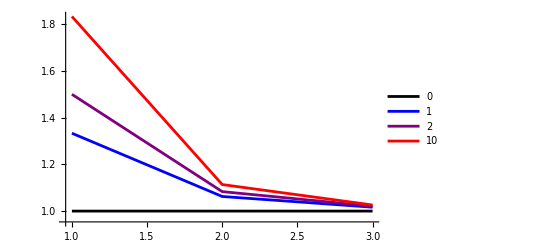

```mathematica
Show[
ListPlot[Table[%260, {α, {0, 1, 2, 10}}],PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,PlotLegends->{0, 1, 2, 10}]
(*Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],*)
(*PlotRange->{Automatic,{0,1}}*)
]
```

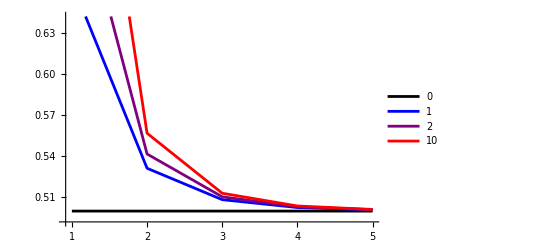

```mathematica
Show[
ListPlot[Table[, {α, {0, 1, 2, 10}}],PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,PlotLegends->{0, 1, 2, 10}]
(*Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],*)
(*PlotRange->{Automatic,{0,1}}*)
]
```

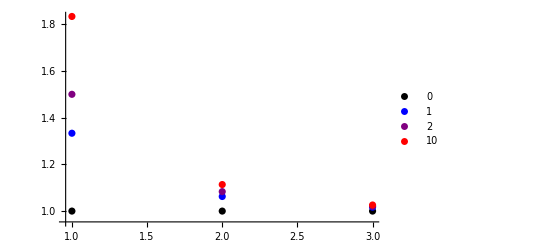

```mathematica
Show[
ListPlot[Table[%260, {α, {0, 1, 2, 10}}],PlotStyle->{{Black},{Blue},{Purple},{Red}},PlotLegends->{0, 1, 2, 10}]
(*Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],*)
(*PlotRange->{Automatic,{0,1}}*)
]
```

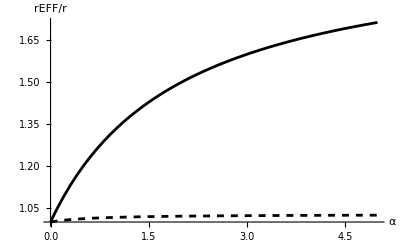

```mathematica
Show[
Plot[(expectedrf[1] * 2r)/r,{α,0,5},PlotStyle->Black],
Plot[reff/r,{α,0,5},PlotStyle->{Black,Dashed}],
AxesLabel->{"α","rEFF/r"}
]
```

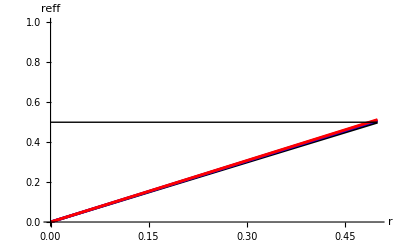

```mathematica
Show[
Plot[Evaluate[reff/.α->{0,1,2,10}],{r,0,1/2},AxesLabel->{"r","reff"},PlotStyle->{{Black},{Blue},{Purple},{Red}}],
Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],
PlotRange->{Automatic,{0,1}}
]
```

#### messing around with analytical formulations

```mathematica
recstate = {0, 0, 1, 1};
recstate // MatrixForm
```

(0
0
1
1)

```mathematica
i = IdentityMatrix[4];
i // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
i * recstate // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
%294 * i // MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
swap23 = {i[[1]], i[[3]], i[[2]], i[[4]]};
swap23 //MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
{i[[4]], i[[2]], i[[3]], i[[1]]} . swap23 . swap23 . swap23 . {0, 0, 1, 1} // MatrixForm
```

(1
1
0
0)

```mathematica
t=Array[y,{4,4}]
```

{{y[1,1],y[1,2],y[1,3],y[1,4]},{y[2,1],y[2,2],y[2,3],y[2,4]},{y[3,1],y[3,2],y[3,3],y[3,4]},{y[4,1],y[4,2],y[4,3],y[4,4]}}

```mathematica
Solve[t.{a, b, c, d} == {a, b, 1-c, 1-d}, Flatten[t]] /. {
y[i_, 1] :> 0,
y[i_, 2] :> 0,
y[i_, 3] :> 0
} // MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(y[1,4]→a/d | y[2,4]→b/d | y[3,4]→-(-1+c)/d | y[4,4]→-(-1+d)/d)

```mathematica
{0, 0, 1, 1}, {1, 0, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {0, 1, 1, 0}, {1, 1, 0, 0}
```

#### With one crossover

With exactly one crossover event, the chromatid states are:

```mathematica
tabEVENTS={{0,1,1,0}}; (* Number of crossover events between the ends*)
tabMATCHES={{1,0,0,1}}; (* Whether markers match at the ends (0=no)*)
```

```mathematica
tabBIAS=({1,1,1,1}+tabEVENTS[[1]]*α)/Total[{1,1,1,1}+tabEVENTS[[1]]*α]
```

{1/(4+2 α),(1+α)/(4+2 α),(1+α)/(4+2 α),1/(4+2 α)}

When a chromatid is chosen, the following determines if it looks recombinant, given one cross-over event:

```mathematica
tabBIAS*({1,1,1,1}-tabMATCHES[[1]])//Total
```

(2 (1+α))/(4+2 α)

If there was an 2r chance of 1 crossover (so that each chromatid has a chance of r of having one crossover) and otherwise no recombination events, then bias will change this by an amount:

```mathematica
rEFF=2*r*%
```

(4 r (1+α))/(4+2 α)

In the absence of a bias:

```mathematica
%/.α->0
```

r

In the limit, as α goes to infinity, then the max rEFF would be 2r, which will rise above one for r values >0.25.

So relative to the expected recombination rat

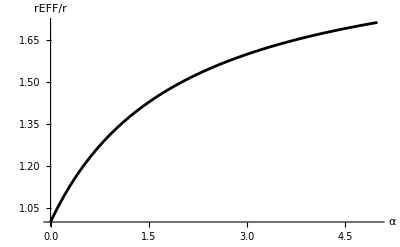

```mathematica
Show[
Plot[rEFF/r,{α,0,5},PlotStyle->Black],
AxesLabel->{"α","rEFF/r"}
]
```

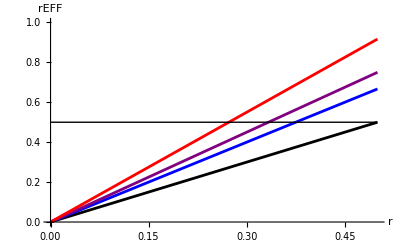

```mathematica
Show[
Plot[Evaluate[rEFF/.α->{0,1,2,10}],{r,0,1/2},AxesLabel->{"r","rEFF"},PlotStyle->{{Black},{Blue},{Purple},{Red}}],
Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],
PlotRange->{Automatic,{0,1}}
]
```

#### With two crossovers

With exactly two crossover events, the chromatid states are:

```mathematica
tabEVENTS={{2,2,0,0},{1,1,1,1},{2,1,1,0}}; (* Number of crossover events between the ends*)
tabMATCHES={{1,1,1,1},{0,0,0,0},{0,1,0,1}}; (* Whether markers match at the ends (0=no)*)
tabCOUNTS={4,4,8};
tabCOUNTS=tabCOUNTS/Total[tabCOUNTS];
```

```mathematica
For[ii=1;rEFFTAB={},ii≤Length[tabCOUNTS],ii++,
tabBIAS=({1,1,1,1}+tabEVENTS[[ii]]*α)/Total[{1,1,1,1}+tabEVENTS[[ii]]*α];
temp=tabBIAS*({1,1,1,1}-tabMATCHES[[ii]])//Total;
rEFFTAB=AppendTo[rEFFTAB,r2*temp]
]
```

```mathematica
rEFFTAB//Factor
```

{0,r2,(r2 (2+3 α))/(4 (1+α))}

Check, but with two crossover events, the average number of matches is 1/2 (in the absence of bias):

```mathematica
Table[tabCOUNTS[[i]]Mean[({1,1,1,1}-tabMATCHES[[i]])],{i,1,Length[tabCOUNTS]}]//Total
```

1/2

where r2 is some function relating the recombination rate r to the chance of two recombination events. 
For example, if there were only 0 or two recombination events (never one), then the average observed recombination rate between markers (no bias) would be p0*0+p2*1/2. Setting p2=1-p0, we would have to have p2 = 2 r (just like with one crossover) to have an average recombination rate in the region of r.

If there was a 2r chance of 2 crossovers (so that each chromatid has a chance of r of having the markers not match) and otherwise no recombination events, then bias will change this by an amount:

```mathematica
rEFF2=tabCOUNTS*rEFFTAB/.r2->2 r//Total//Factor
```

(r (4+5 α))/(4 (1+α))

In the absence of a bias:

```mathematica
%/.α->0
```

r

In the limit, as α goes to infinity, then the max rEFF would be 5r/4, which will rise above one for r values >0.8.  This (dashed) is much less biased than with a single cross-over (solid black), even though we have allowed an additive rise in preference with the number of crossover events.

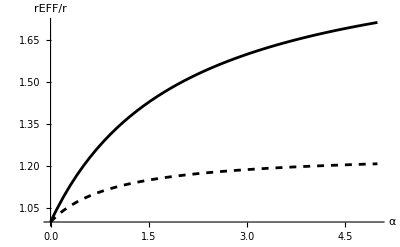

```mathematica
Show[
Plot[rEFF/r,{α,0,5},PlotStyle->Black],
Plot[rEFF2/r,{α,0,5},PlotStyle->{Black,Dashed}],
AxesLabel->{"α","rEFF/r"}
]
```

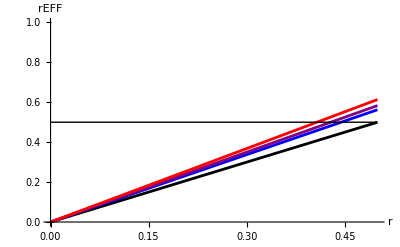

```mathematica
Show[
Plot[Evaluate[rEFF2/.α->{0,1,2,10}],{r,0,1/2},AxesLabel->{"r","rEFF"},PlotStyle->{{Black},{Blue},{Purple},{Red}}],
Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],
PlotRange->{Automatic,{0,1}}
]
```

With exactly two crossover events, the chromatid states are:

```mathematica
tabEVENTS={{2,2,0,0},{1,1,1,1},{2,1,1,0}}; (* Number of crossover events between the ends*)
tabMATCHES={{1,1,1,1},{0,0,0,0},{0,1,0,1}}; (* Whether markers match at the ends (0=no)*)
tabCOUNTS={4,4,8};
tabCOUNTS=tabCOUNTS/Total[tabCOUNTS];
```

```mathematica
For[ii=1;rEFFTAB={},ii≤Length[tabCOUNTS],ii++,
tabBIAS=({1,1,1,1}+tabEVENTS[[ii]]*α)/Total[{1,1,1,1}+tabEVENTS[[ii]]*α];
temp=tabBIAS*({1,1,1,1}-tabMATCHES[[ii]])//Total;
rEFFTAB=AppendTo[rEFFTAB,r2*temp]
]
```

```mathematica
rEFFTAB//Factor
```

{0,r2,(r2 (2+3 α))/(4 (1+α))}

Check, but with two crossover events, the average number of matches is 1/2 (in the absence of bias):

```mathematica
Table[tabCOUNTS[[i]]Mean[({1,1,1,1}-tabMATCHES[[i]])],{i,1,Length[tabCOUNTS]}]//Total
```

1/2

where r2 is some function relating the recombination rate r to the chance of two recombination events. 
For example, if there were only 0 or two recombination events (never one), then the average observed recombination rate between markers (no bias) would be p0*0+p2*1/2. Setting p2=1-p0, we would have to have p2 = 2 r (just like with one crossover) to have an average recombination rate in the region of r.

If there was a 2r chance of 2 crossovers (so that each chromatid has a chance of r of having the markers not match) and otherwise no recombination events, then bias will change this by an amount:

```mathematica
rEFF2=tabCOUNTS*rEFFTAB/.r2->2 r//Total//Factor
```

(r (4+5 α))/(4 (1+α))

In the absence of a bias:

```mathematica
%/.α->0
```

r

In the limit, as α goes to infinity, then the max rEFF would be 5r/4, which will rise above one for r values >0.8.  This (dashed) is much less biased than with a single cross-over (solid black), even though we have allowed an additive rise in preference with the number of crossover events.

```mathematica
Show[
Plot[rEFF/r,{α,0,5},PlotStyle->Black],
Plot[rEFF2/r,{α,0,5},PlotStyle->{Black,Dashed}],
AxesLabel->{"α","rEFF/r"}
]
```

-Graphics-

```mathematica
Show[
Plot[Evaluate[rEFF2/.α->{0,1,2,10}],{r,0,1/2},AxesLabel->{"r","rEFF"},PlotStyle->{{Black},{Blue},{Purple},{Red}}],
Plot[1/2,{r,0,1/2},PlotStyle->{{Black,Thin}}],
PlotRange->{Automatic,{0,1}}
]
```

-Graphics-

#### Automating

```mathematica
family={{1,3},{1,4},{2,3},{2,4}};
origin={{1},{1},{0},{0}} (*Labeling chromatids by their sister state near the centromere*)
```

{{1},{1},{0},{0}}

```mathematica
numrec=1;
```

```mathematica
For[rr=1,rr≤numrec,rr++,
For[ff=1,ff≤Length[family],ff++,
genotype[ff]=origin;
add=Last[Transpose[genotype[ff]]];
switch1=add[[family[[ff]][[1]]]];
switch2=add[[family[[ff]][[2]]]];
add[[family[[ff]][[1]]]]=switch2;
add[[family[[ff]][[2]]]]=switch1;
genotype[ff]=Transpose[Join[Transpose[genotype[ff]],{add}]]
]
]
```

```mathematica
genotype[4]
```

{{1,1},{1,0},{0,0},{0,1}}

#### weight function

```mathematica
testtab={{0,1,1,0}};
```

```mathematica
({1, 1, 1, 1} + {0, 0, 0, 1}*α)/Total[{1, 1, 1, 1} + {0, 0, 0, 1}*α]
```

{1/(4+α),1/(4+α),1/(4+α),(1+α)/(4+α)}

```mathematica
wα[x_] = (1+ x*α)/Total[1 + x*α];
```

```mathematica
wα[{0, 0, 0, 1}]
```

{1/(4+α),1/(4+α),1/(4+α),(1+α)/(4+α)}

### a matrix for determining next-match-state?

rules (both markers on same side of centromere):
- if 0-0, then 1-1
- if 1-1, then 0, 0
- if 1-0 or 0-1, then 1-0 or 0-1

rules (both markers on diff side of centromere):

```mathematica
solve
```

solve

## old

```mathematica
Clear[n]
```

```mathematica
n=2;
```

```mathematica
configuration=Flatten[Table[{i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,2,0,0},{1,1,0,0},{2,0,0,0},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{0,0,0,2},{0,0,1,1},{0,0,2,0}}

We can also break this apart into how many times chromatids {1,2,3,4} were involved:

```mathematica
strand=Flatten[Table[{n-k,k,i+j,n-i-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{2,0,0,2},{2,0,1,1},{2,0,2,0},{1,1,0,2},{1,1,1,1},{1,1,1,1},{1,1,2,0},{0,2,0,2},{0,2,1,1},{0,2,2,0}}

```mathematica
likelihood=Flatten[Table[PDF[BinomialDistribution[n,p],k]PDF[BinomialDistribution[k,p],j]PDF[BinomialDistribution[n-k,p],i] ,{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{(1-p)^4,2 (1-p)^3 p,(1-p)^2 p^2,2 (1-p)^3 p,2 (1-p)^2 p^2,2 (1-p)^2 p^2,2 (1-p) p^3,(1-p)^2 p^2,2 (1-p) p^3,p^4}

```mathematica
MatrixForm[{configuration,likelihood}]
```

({0,2,0,0} | {1,1,0,0} | {2,0,0,0} | {0,1,0,1} | {0,1,1,0} | {1,0,0,1} | {1,0,1,0} | {0,0,0,2} | {0,0,1,1} | {0,0,2,0}
(1-p)^4 | 2 (1-p)^3 p | (1-p)^2 p^2 | 2 (1-p)^3 p | 2 (1-p)^2 p^2 | 2 (1-p)^2 p^2 | 2 (1-p) p^3 | (1-p)^2 p^2 | 2 (1-p) p^3 | p^4)

```mathematica
likelihood/.p->1/2
```

{1/16,1/8,1/16,1/8,1/8,1/8,1/8,1/16,1/8,1/16}

```mathematica
Clear[n]
```

```mathematica
n=3;
```

```mathematica
configuration=Flatten[Table[{i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,3,0,0},{1,2,0,0},{2,1,0,0},{3,0,0,0},{0,2,0,1},{0,2,1,0},{1,1,0,1},{1,1,1,0},{2,0,0,1},{2,0,1,0},{0,1,0,2},{0,1,1,1},{0,1,2,0},{1,0,0,2},{1,0,1,1},{1,0,2,0},{0,0,0,3},{0,0,1,2},{0,0,2,1},{0,0,3,0}}

We can also break this apart into how many times chromatids {1,2,3,4} were involved:

```mathematica
strand=Flatten[Table[{n-k,k,i+j,n-i-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{3,0,0,3},{3,0,1,2},{3,0,2,1},{3,0,3,0},{2,1,0,3},{2,1,1,2},{2,1,1,2},{2,1,2,1},{2,1,2,1},{2,1,3,0},{1,2,0,3},{1,2,1,2},{1,2,2,1},{1,2,1,2},{1,2,2,1},{1,2,3,0},{0,3,0,3},{0,3,1,2},{0,3,2,1},{0,3,3,0}}

```mathematica
likelihood=Flatten[Table[PDF[BinomialDistribution[n,p],k]PDF[BinomialDistribution[k,p],j]PDF[BinomialDistribution[n-k,p],i] ,{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{(1-p)^6,3 (1-p)^5 p,3 (1-p)^4 p^2,(1-p)^3 p^3,3 (1-p)^5 p,3 (1-p)^4 p^2,6 (1-p)^4 p^2,6 (1-p)^3 p^3,3 (1-p)^3 p^3,3 (1-p)^2 p^4,3 (1-p)^4 p^2,6 (1-p)^3 p^3,3 (1-p)^2 p^4,3 (1-p)^3 p^3,6 (1-p)^2 p^4,3 (1-p) p^5,(1-p)^3 p^3,3 (1-p)^2 p^4,3 (1-p) p^5,p^6}

```mathematica
MatrixForm[{configuration,likelihood}]
```

({0,3,0,0} | {1,2,0,0} | {2,1,0,0} | {3,0,0,0} | {0,2,0,1} | {0,2,1,0} | {1,1,0,1} | {1,1,1,0} | {2,0,0,1} | {2,0,1,0} | {0,1,0,2} | {0,1,1,1} | {0,1,2,0} | {1,0,0,2} | {1,0,1,1} | {1,0,2,0} | {0,0,0,3} | {0,0,1,2} | {0,0,2,1} | {0,0,3,0}
(1-p)^6 | 3 (1-p)^5 p | 3 (1-p)^4 p^2 | (1-p)^3 p^3 | 3 (1-p)^5 p | 3 (1-p)^4 p^2 | 6 (1-p)^4 p^2 | 6 (1-p)^3 p^3 | 3 (1-p)^3 p^3 | 3 (1-p)^2 p^4 | 3 (1-p)^4 p^2 | 6 (1-p)^3 p^3 | 3 (1-p)^2 p^4 | 3 (1-p)^3 p^3 | 6 (1-p)^2 p^4 | 3 (1-p) p^5 | (1-p)^3 p^3 | 3 (1-p)^2 p^4 | 3 (1-p) p^5 | p^6)

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,p],k]PDF[BinomialDistribution[k,p],j]PDF[BinomialDistribution[n-k,p],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,3 (1-p)^6,0,0},{3 (1-p)^5 p,6 (1-p)^5 p,0,0},{6 (1-p)^4 p^2,3 (1-p)^4 p^2,0,0},{3 (1-p)^3 p^3,0,0,0},{0,6 (1-p)^5 p,0,3 (1-p)^5 p},{0,6 (1-p)^4 p^2,3 (1-p)^4 p^2,0},{6 (1-p)^4 p^2,6 (1-p)^4 p^2,0,6 (1-p)^4 p^2},{6 (1-p)^3 p^3,6 (1-p)^3 p^3,6 (1-p)^3 p^3,0},{6 (1-p)^3 p^3,0,0,3 (1-p)^3 p^3},{6 (1-p)^2 p^4,0,3 (1-p)^2 p^4,0},{0,3 (1-p)^4 p^2,0,6 (1-p)^4 p^2},{0,6 (1-p)^3 p^3,6 (1-p)^3 p^3,6 (1-p)^3 p^3},{0,3 (1-p)^2 p^4,6 (1-p)^2 p^4,0},{3 (1-p)^3 p^3,0,0,6 (1-p)^3 p^3},{6 (1-p)^2 p^4,0,6 (1-p)^2 p^4,6 (1-p)^2 p^4},{3 (1-p) p^5,0,6 (1-p) p^5,0},{0,0,0,3 (1-p)^3 p^3},{0,0,3 (1-p)^2 p^4,6 (1-p)^2 p^4},{0,0,6 (1-p) p^5,3 (1-p) p^5},{0,0,3 p^6,0}}

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,3/64,0,0},{3/64,3/32,0,0},{3/32,3/64,0,0},{3/64,0,0,0},{0,3/32,0,3/64},{0,3/32,3/64,0},{3/32,3/32,0,3/32},{3/32,3/32,3/32,0},{3/32,0,0,3/64},{3/32,0,3/64,0},{0,3/64,0,3/32},{0,3/32,3/32,3/32},{0,3/64,3/32,0},{3/64,0,0,3/32},{3/32,0,3/32,3/32},{3/64,0,3/32,0},{0,0,0,3/64},{0,0,3/64,3/32},{0,0,3/32,3/64},{0,0,3/64,0}}

```mathematica
%//Total
```

{3/4,3/4,3/4,3/4}

This correctly gives a total number of crossovers of three, summed over events involving {13,14,23,24} chromatids.

```mathematica
Sum[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}]
```

{3/4,3/4,3/4,3/4}

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] Sort[{i,n-k-i,j,k-j}],{k,0,n},{i,0,n-k},{j,0,k}],2]//Tally
```

{{{0,0,0,3/64},4},{{0,0,3/64,3/32},12},{{0,3/32,3/32,3/32},4}}

```mathematica
Clear[n]
```

```mathematica
n=4;
```

```mathematica
configuration=Flatten[Table[{i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,4,0,0},{1,3,0,0},{2,2,0,0},{3,1,0,0},{4,0,0,0},{0,3,0,1},{0,3,1,0},{1,2,0,1},{1,2,1,0},{2,1,0,1},{2,1,1,0},{3,0,0,1},{3,0,1,0},{0,2,0,2},{0,2,1,1},{0,2,2,0},{1,1,0,2},{1,1,1,1},{1,1,2,0},{2,0,0,2},{2,0,1,1},{2,0,2,0},{0,1,0,3},{0,1,1,2},{0,1,2,1},{0,1,3,0},{1,0,0,3},{1,0,1,2},{1,0,2,1},{1,0,3,0},{0,0,0,4},{0,0,1,3},{0,0,2,2},{0,0,3,1},{0,0,4,0}}

We can also break this apart into how many times chromatids {1,2,3,4} were involved:

```mathematica
strand=Flatten[Table[{n-k,k,i+j,n-i-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{4,0,0,4},{4,0,1,3},{4,0,2,2},{4,0,3,1},{4,0,4,0},{3,1,0,4},{3,1,1,3},{3,1,1,3},{3,1,2,2},{3,1,2,2},{3,1,3,1},{3,1,3,1},{3,1,4,0},{2,2,0,4},{2,2,1,3},{2,2,2,2},{2,2,1,3},{2,2,2,2},{2,2,3,1},{2,2,2,2},{2,2,3,1},{2,2,4,0},{1,3,0,4},{1,3,1,3},{1,3,2,2},{1,3,3,1},{1,3,1,3},{1,3,2,2},{1,3,3,1},{1,3,4,0},{0,4,0,4},{0,4,1,3},{0,4,2,2},{0,4,3,1},{0,4,4,0}}

```mathematica
likelihood=Flatten[Table[PDF[BinomialDistribution[n,p],k]PDF[BinomialDistribution[k,p],j]PDF[BinomialDistribution[n-k,p],i] ,{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{(1-p)^8,4 (1-p)^7 p,6 (1-p)^6 p^2,4 (1-p)^5 p^3,(1-p)^4 p^4,4 (1-p)^7 p,4 (1-p)^6 p^2,12 (1-p)^6 p^2,12 (1-p)^5 p^3,12 (1-p)^5 p^3,12 (1-p)^4 p^4,4 (1-p)^4 p^4,4 (1-p)^3 p^5,6 (1-p)^6 p^2,12 (1-p)^5 p^3,6 (1-p)^4 p^4,12 (1-p)^5 p^3,24 (1-p)^4 p^4,12 (1-p)^3 p^5,6 (1-p)^4 p^4,12 (1-p)^3 p^5,6 (1-p)^2 p^6,4 (1-p)^5 p^3,12 (1-p)^4 p^4,12 (1-p)^3 p^5,4 (1-p)^2 p^6,4 (1-p)^4 p^4,12 (1-p)^3 p^5,12 (1-p)^2 p^6,4 (1-p) p^7,(1-p)^4 p^4,4 (1-p)^3 p^5,6 (1-p)^2 p^6,4 (1-p) p^7,p^8}

```mathematica
MatrixForm[{configuration,likelihood}]
```

({0,4,0,0} | {1,3,0,0} | {2,2,0,0} | {3,1,0,0} | {4,0,0,0} | {0,3,0,1} | {0,3,1,0} | {1,2,0,1} | {1,2,1,0} | {2,1,0,1} | {2,1,1,0} | {3,0,0,1} | {3,0,1,0} | {0,2,0,2} | {0,2,1,1} | {0,2,2,0} | {1,1,0,2} | {1,1,1,1} | {1,1,2,0} | {2,0,0,2} | {2,0,1,1} | {2,0,2,0} | {0,1,0,3} | {0,1,1,2} | {0,1,2,1} | {0,1,3,0} | {1,0,0,3} | {1,0,1,2} | {1,0,2,1} | {1,0,3,0} | {0,0,0,4} | {0,0,1,3} | {0,0,2,2} | {0,0,3,1} | {0,0,4,0}
(1-p)^8 | 4 (1-p)^7 p | 6 (1-p)^6 p^2 | 4 (1-p)^5 p^3 | (1-p)^4 p^4 | 4 (1-p)^7 p | 4 (1-p)^6 p^2 | 12 (1-p)^6 p^2 | 12 (1-p)^5 p^3 | 12 (1-p)^5 p^3 | 12 (1-p)^4 p^4 | 4 (1-p)^4 p^4 | 4 (1-p)^3 p^5 | 6 (1-p)^6 p^2 | 12 (1-p)^5 p^3 | 6 (1-p)^4 p^4 | 12 (1-p)^5 p^3 | 24 (1-p)^4 p^4 | 12 (1-p)^3 p^5 | 6 (1-p)^4 p^4 | 12 (1-p)^3 p^5 | 6 (1-p)^2 p^6 | 4 (1-p)^5 p^3 | 12 (1-p)^4 p^4 | 12 (1-p)^3 p^5 | 4 (1-p)^2 p^6 | 4 (1-p)^4 p^4 | 12 (1-p)^3 p^5 | 12 (1-p)^2 p^6 | 4 (1-p) p^7 | (1-p)^4 p^4 | 4 (1-p)^3 p^5 | 6 (1-p)^2 p^6 | 4 (1-p) p^7 | p^8)

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,p],k]PDF[BinomialDistribution[k,p],j]PDF[BinomialDistribution[n-k,p],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,4 (1-p)^8,0,0},{4 (1-p)^7 p,12 (1-p)^7 p,0,0},{12 (1-p)^6 p^2,12 (1-p)^6 p^2,0,0},{12 (1-p)^5 p^3,4 (1-p)^5 p^3,0,0},{4 (1-p)^4 p^4,0,0,0},{0,12 (1-p)^7 p,0,4 (1-p)^7 p},{0,12 (1-p)^6 p^2,4 (1-p)^6 p^2,0},{12 (1-p)^6 p^2,24 (1-p)^6 p^2,0,12 (1-p)^6 p^2},{12 (1-p)^5 p^3,24 (1-p)^5 p^3,12 (1-p)^5 p^3,0},{24 (1-p)^5 p^3,12 (1-p)^5 p^3,0,12 (1-p)^5 p^3},{24 (1-p)^4 p^4,12 (1-p)^4 p^4,12 (1-p)^4 p^4,0},{12 (1-p)^4 p^4,0,0,4 (1-p)^4 p^4},{12 (1-p)^3 p^5,0,4 (1-p)^3 p^5,0},{0,12 (1-p)^6 p^2,0,12 (1-p)^6 p^2},{0,24 (1-p)^5 p^3,12 (1-p)^5 p^3,12 (1-p)^5 p^3},{0,12 (1-p)^4 p^4,12 (1-p)^4 p^4,0},{12 (1-p)^5 p^3,12 (1-p)^5 p^3,0,24 (1-p)^5 p^3},{24 (1-p)^4 p^4,24 (1-p)^4 p^4,24 (1-p)^4 p^4,24 (1-p)^4 p^4},{12 (1-p)^3 p^5,12 (1-p)^3 p^5,24 (1-p)^3 p^5,0},{12 (1-p)^4 p^4,0,0,12 (1-p)^4 p^4},{24 (1-p)^3 p^5,0,12 (1-p)^3 p^5,12 (1-p)^3 p^5},{12 (1-p)^2 p^6,0,12 (1-p)^2 p^6,0},{0,4 (1-p)^5 p^3,0,12 (1-p)^5 p^3},{0,12 (1-p)^4 p^4,12 (1-p)^4 p^4,24 (1-p)^4 p^4},{0,12 (1-p)^3 p^5,24 (1-p)^3 p^5,12 (1-p)^3 p^5},{0,4 (1-p)^2 p^6,12 (1-p)^2 p^6,0},{4 (1-p)^4 p^4,0,0,12 (1-p)^4 p^4},{12 (1-p)^3 p^5,0,12 (1-p)^3 p^5,24 (1-p)^3 p^5},{12 (1-p)^2 p^6,0,24 (1-p)^2 p^6,12 (1-p)^2 p^6},{4 (1-p) p^7,0,12 (1-p) p^7,0},{0,0,0,4 (1-p)^4 p^4},{0,0,4 (1-p)^3 p^5,12 (1-p)^3 p^5},{0,0,12 (1-p)^2 p^6,12 (1-p)^2 p^6},{0,0,12 (1-p) p^7,4 (1-p) p^7},{0,0,4 p^8,0}}

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}],2]
```

{{0,1/64,0,0},{1/64,3/64,0,0},{3/64,3/64,0,0},{3/64,1/64,0,0},{1/64,0,0,0},{0,3/64,0,1/64},{0,3/64,1/64,0},{3/64,3/32,0,3/64},{3/64,3/32,3/64,0},{3/32,3/64,0,3/64},{3/32,3/64,3/64,0},{3/64,0,0,1/64},{3/64,0,1/64,0},{0,3/64,0,3/64},{0,3/32,3/64,3/64},{0,3/64,3/64,0},{3/64,3/64,0,3/32},{3/32,3/32,3/32,3/32},{3/64,3/64,3/32,0},{3/64,0,0,3/64},{3/32,0,3/64,3/64},{3/64,0,3/64,0},{0,1/64,0,3/64},{0,3/64,3/64,3/32},{0,3/64,3/32,3/64},{0,1/64,3/64,0},{1/64,0,0,3/64},{3/64,0,3/64,3/32},{3/64,0,3/32,3/64},{1/64,0,3/64,0},{0,0,0,1/64},{0,0,1/64,3/64},{0,0,3/64,3/64},{0,0,3/64,1/64},{0,0,1/64,0}}

```mathematica
%//Total
```

{1,1,1,1}

This correctly gives a total number of crossovers of three, summed over events involving {13,14,23,24} chromatids.

```mathematica
Sum[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] {i,n-k-i,j,k-j},{k,0,n},{i,0,n-k},{j,0,k}]
```

{1,1,1,1}

```mathematica
Flatten[Table[PDF[BinomialDistribution[n,1/2],k]PDF[BinomialDistribution[k,1/2],j]PDF[BinomialDistribution[n-k,1/2],i] Sort[{i,n-k-i,j,k-j}],{k,0,n},{i,0,n-k},{j,0,k}],2]//Tally
```

{{{0,0,0,1/64},4},{{0,0,1/64,3/64},12},{{0,0,3/64,3/64},6},{{0,3/64,3/64,3/32},12},{{3/32,3/32,3/32,3/32},1}}

```mathematica
f[x_] := x^2
```

```mathematica
f'[x]
```

2 x

```mathematica
curr = strand[[2]]
```

{4,0,1,3}

```mathematica
curr / Dot[curr, {1, 1, 1, 1}]
```

{1/2,0,1/8,3/8}

so to weight the strands by drive, if the drive is proportional, the function just divides the strand config count vector by the dot product of itself and {1, 1, 1, 1}. what about non-proportional drive?

```mathematica
curr
```

{4,0,1,3}

```mathematica
Sign[curr] / Total[Sign[curr]]
```

{1/3,0,1/3,1/3}

what counts as a “function” for our purposes?

```mathematica
wprop[x_] := x / Total[x];
wnonprop[x_] := Sign[x] / Total[Sign[x]];
```

```mathematica
wprop[curr]
```

{1/2,0,1/8,3/8}

```mathematica
wnonprop[curr]
```

{1/3,0,1/3,1/3}

### order of CO placements matters

consider two crossovers, with strand-configuration 1,3 and 2,3. the chromatids start out like so:

#### case II: 2,3 -> 1,3

first crossover: 2,3:

```mathematica
.---|---
.---|xxx    <-
.xxx|---    <-
.xxx|xxx
```

second crossover: 1,3:

```mathematica
.----|--    <-
.---x|xx
.xxx-|--    <-
.xxxx|xx
```

so crossover order matters (even if location + strand configuration + CO count per chromatid is the same, order of placement can change what haplotype arrangements we get).
how do we handle this?

in the example above, the change in RF is the same: the double-CO chromatid has no visible CO, and neither does the chromatid with the single sister-CO. can we use this to disregard the diff haplotype arrangements?
-> i don’t think so, bc the non-visible COs still affect drive

```mathematica
curr
```

{4,0,1,3}

let RFc be the part of RF determined just from the chromatid configuration (not weighted by P(crossover in region) or P(recovery)). then:
- RFc is fully determined by the match-mismatch state
- RFc 
- the current match-mismatch state + the next pair fully determines the next match-mismatch state
- what gets “recombined away”?
	- presumably, part from centromere->telomere (centromere never gets “recombined away”)?
	- assume acrocentric chromosome for now
- (1) match-mismatch is order-sensitive, but not location-sensitive
- (2) events-per-chromatid is location-sensitive, but not order-sensitive
- from (1) and (2), neither match-mismatch state nor events-per-chromatid can be determined from pair-conf + strand-conf alone
- we need both match-mismatch and events-per-chromatid: match-mismatch => RF, events-per-chromatid => drive weights

RF is from P(recomb), match-mismatch state, P(recovery)
match-mismatch state: doesn’t matter where you place COs, but order of pair involvement matters!!
	depending on what gets “recombied away”, could also be location-sensitive
for P(recovery), need COs-per-strand
	HOWEVER: not necessarily recoverable from pair-conf, since COs can be “recombined away”!!

#### wip:matrix-based model

let  be a random variable that takes values in  with equal probability, indicating the chromatid pair participating in the CO.

we define “swap matrices” , where  is the 4x4 identity matrix with rows  and  swapped, and :

```mathematica
Imat = IdentityMatrix[4]
S13 = Permute[Imat, Cycles[{{1, 3}}]]
S14 = Permute[Imat, Cycles[{{1, 4}}]]
S23 = Permute[Imat, Cycles[{{2, 3}}]]
S24 = Permute[Imat, Cycles[{{2, 4}}]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}

{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,0,0}}

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

then let  be a random variable that takes on values  or  based on the value of :

expectation of M:

```mathematica
0.25 * {S13, S14, S23, S24} // Total
```

{{0.5,0.,0.25,0.25},{0.,0.5,0.25,0.25},{0.25,0.25,0.5,0.},{0.25,0.25,0.,0.5}}

```mathematica
%422 // MatrixForm
```

(0.5 | 0. | 0.25 | 0.25
0. | 0.5 | 0.25 | 0.25
0.25 | 0.25 | 0.5 | 0.
0.25 | 0.25 | 0. | 0.5)

```mathematica
% // Eigenvalues
```

{1.,0.5,0.5,-2.64873×10^-17}

```mathematica
Clear[n];
```

```mathematica
TransformedDistribution[MatrixPower[, n], n \[Distributed] PoissonDistribution[λ]]
```

TransformedDistribution[{{0.25+0.25 (6.66134×10^-16)^x+0.5 0.5^x+3.11264×10^-31 0.5^x,0.25+0.25 (6.66134×10^-16)^x-0.5 0.5^x+2.74645×10^-31 0.5^x,0.25-0.25 (6.66134×10^-16)^x-1.431×10^-16 0.5^x+3.29837×10^-16 0.5^x,0.25-0.25 (6.66134×10^-16)^x-1.86714×10^-17 0.5^x-3.29837×10^-16 0.5^x},{0.25+0.25 (6.66134×10^-16)^x-0.5 0.5^x+2.3718×10^-31 0.5^x,0.25+0.25 (6.66134×10^-16)^x+0.5^(1+x)+2.09276×10^-31 0.5^x,0.25-0.25 (6.66134×10^-16)^x+1.431×10^-16 0.5^x+2.51333×10^-16 0.5^x,0.25-0.25 (6.66134×10^-16)^x+1.86714×10^-17 0.5^x-2.51333×10^-16 0.5^x},{0.25-0.25 (6.66134×10^-16)^x-6.26858×10^-17 0.5^x+4.71845×10^-16 0.5^x,0.25-0.25 (6.66134×10^-16)^x+6.26858×10^-17 0.5^x+4.16334×10^-16 0.5^x,0.25+0.25 (6.66134×10^-16)^x+1.79407×10^-32 0.5^x+0.5 0.5^x,0.25+0.25 (6.66134×10^-16)^x+2.34087×10^-33 0.5^x-0.5 0.5^x},{0.25-0.25 (6.66134×10^-16)^x-4.71845×10^-16 0.5^x,0.25-0.25 (6.66134×10^-16)^x-4.16334×10^-16 0.5^x,0.25+0.25 (6.66134×10^-16)^x-0.5 0.5^x,0.25+0.25 (6.66134×10^-16)^x+0.5 0.5^x}},x\[Distributed]PoissonDistribution[λ]]

## new strand invasion model

let n be the number of COs the tetrad experiences. we represent the number of COs on each chromatid with variables x1, x2, x3, x4:

```mathematica
{x1, x2, x3, x4}
```

{x1,n-x1,x3,n-x3}

x1 and x3 are binomially distributed, and they fully determine x2 and x4 respectively:

```mathematica
px1 = BinomialDistribution[n, 1/2];
px3 = BinomialDistribution[n, 1/2];
x2 =  n - x1;
x4 = n - x3;
```

since x1 and x3 are independent, we can find the joint distribution for all 4 chromatids:

```mathematica
pxall = ProductDistribution[px1, px3]
```

ProductDistribution[BinomialDistribution[n,1/2],BinomialDistribution[n,1/2]]

### additive drive

we define a function that additively weights the number of COs per chromatid by α, and then multiplies that by 1 if the chromatid is recombinant (and 0 otherwise):

```mathematica
wαAdd[y_]:= (1+α*y)/(4+Sum[(α *y)[[k]], {k, 1, 4}]) * Mod[y, 2]
```

and then we define a function that sums the application of this function across all chromatids:

```mathematica
g[y_]:= wαAdd[y] // Total
```

then  is a random variable representing the proportion of recovered chromatids that are recombinant:

```mathematica
mAdd = g[{x1, x2, x3, x4}]
```

((1+(n-x1) α) Mod[n-x1,2])/(4+(n-x1) α+x1 α+(n-x3) α+x3 α)+((1+x1 α) Mod[x1,2])/(4+(n-x1) α+x1 α+(n-x3) α+x3 α)+((1+(n-x3) α) Mod[n-x3,2])/(4+(n-x1) α+x1 α+(n-x3) α+x3 α)+((1+x3 α) Mod[x3,2])/(4+(n-x1) α+x1 α+(n-x3) α+x3 α)

and r_eff is the expectation of d:

```mathematica
reff[numcos_]:=Expectation[mAdd /. n->numcos, {x1, x3} \[Distributed] pxall /. n->numcos]
```

for n = 1:

```mathematica
reff[1]
```

(1+α)/(2+α)

numerically, it seems like r_eff is the same as r for n > 1:

```mathematica
Table[reff[n], {n, 1, 20}]
```

{(1+α)/(2+α),1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

plotting r_eff over different n, with different lines for different alpha:

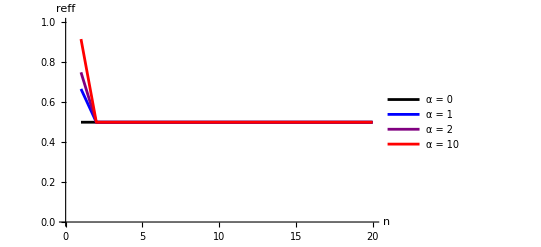

```mathematica
Show[
ListPlot[
Table[, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{"α = 0", "α = 1", "α = 2", "α = 10"},PlotRange->{Automatic,{0,1}},
AxesLabel-> {"n", "reff"}
]
]
```

### does increasing variance lead to different additive drive patterns?

```mathematica
pv1=BetaBinomialDistribution[n,1, 1];
pv3=BetaBinomialDistribution[n,1, 1];
v2=n-v1;
v4=n-v3;
```

```mathematica
pvall = ProductDistribution[pv1, pv3]
```

ProductDistribution[BetaBinomialDistribution[n,1,1],BetaBinomialDistribution[n,1,1]]

```mathematica
mAddVar = g[{v1, v2, v3, v4}]
```

((1+(n-v1) α) Mod[n-v1,2])/(4+(n-v1) α+v1 α+(n-v3) α+v3 α)+((1+v1 α) Mod[v1,2])/(4+(n-v1) α+v1 α+(n-v3) α+v3 α)+((1+(n-v3) α) Mod[n-v3,2])/(4+(n-v1) α+v1 α+(n-v3) α+v3 α)+((1+v3 α) Mod[v3,2])/(4+(n-v1) α+v1 α+(n-v3) α+v3 α)

```mathematica
reffAddVar[numcos_] := Expectation[mAddVar /. n-> numcos, {v1, v3} \[Distributed] pvall]
```

```mathematica
Table[reffAddVar[n], {n, 1, 10}]
```

{(1+α)/(2+α),2/3,1/2,4/5,(3+5 α)/(6+15 α),6/7,(4+7 α)/(8+28 α),8/9,(5+9 α)/(10+45 α),10/11}

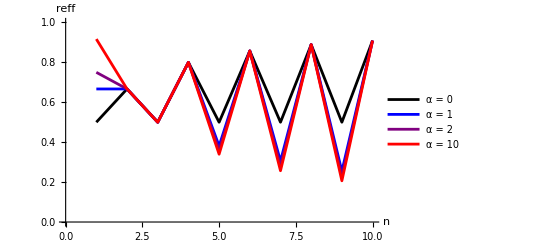

```mathematica
Show[
ListPlot[
Table[, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{"α = 0", "α = 1", "α = 2", "α = 10"},PlotRange->{Automatic,{0,1}},
AxesLabel-> {"n", "reff"}
]
]
```

so causing the number of COs placed on a chromatid to be overdispersed disrupts the “balanced” possibilities and results in oscillation.

### multiplicative drive

we define a function that additively weights the number of COs per chromatid by α, and then multiplies that by 1 if the chromatid is recombinant (and 0 otherwise):

```mathematica
wαMult[y_]:= (1+α)^y/Sum[((1 + α)^y)[[k]], {k, 1, 4}] * Mod[y, 2]
```

and then we define a function that sums the application of this function across all chromatids:

```mathematica
h[y_]:= wαMult[y] // Total
```

is a random variable representing the proportion of recovered chromatids that are recombinant:

```mathematica
mMult = h[{x1, x2, x3, x4}]
```

((1+α)^(n-x1) Mod[n-x1,2])/((1+α)^(n-x1)+(1+α)^x1+(1+α)^(n-x3)+(1+α)^x3)+((1+α)^x1 Mod[x1,2])/((1+α)^(n-x1)+(1+α)^x1+(1+α)^(n-x3)+(1+α)^x3)+((1+α)^(n-x3) Mod[n-x3,2])/((1+α)^(n-x1)+(1+α)^x1+(1+α)^(n-x3)+(1+α)^x3)+((1+α)^x3 Mod[x3,2])/((1+α)^(n-x1)+(1+α)^x1+(1+α)^(n-x3)+(1+α)^x3)

and r_eff is the expectation of m:

```mathematica
reffMult[numcos_]:=Expectation[mMult /. n->numcos, {x1, x3} \[Distributed] pxall /. n->numcos]
```

for n = 1:

```mathematica
reffMult[1]
```

(1+α)/(2+α)

the formulation for larger n is not as clean as for additive drive:

```mathematica
Table[reffMult[n], {n, 1, 8}]//FullSimplify
```

{(1+α)/(2+α),1/4+(1+α)/(2+α)^2,1/48 (21+8/(2+α)+(-1+α)/(1+α+α^2)),(16+α (2+α) (16+5 α (2+α)))/(8 (2+α)^2 (1+α+α^2)),(1965-128/(2+α)-(25 (-1+α))/(1+α+α^2)+(-6+3 α (2+α+α^2))/(1+α (1+α) (2+α (2+α))))/3840,1/256 (64+(150 (1+α))/(2+α)^2+(10 (1+α)^3)/((2+α)^2 (1+α+α^2)^2)+(3 (1+α) (1+(1+α)^4))/(2+α+(1+α)^5+(1+α)^6)+(45 (2+α (2+α) (2+α (2+α))))/((2+α)^2 (1+α+α^2))),(71330+1024/(2+α)+(245 (-1+α))/(1+α+α^2)+(98-49 α (2+α+α^2))/(1+α (1+α) (2+α (2+α)))+(5 (-3+α (3+α (1+α) (3+α (2+α)))))/(1+α (1+α) (1+α+α^2) (3+α (3+α))))/143360,(177660+118784/(2+α)^2-118784/(2+α)-(7350 α)/((1+α+α^2)^2)+(245 (61+91 α))/(1+α+α^2)-(441 (1+α) (4+α (4+11 α)))/(1+α (1+α) (2+α (2+α)))+(45 (1+α) (3+α (6+α (15+α (12+5 α)))))/(1+α (1+α) (1+α+α^2) (3+α (3+α))))/322560}

when numericized for a given α, we can see some oscillation around 1/2:

```mathematica
/. α -> 10 // Map[N]
```

{0.916667,0.326389,0.453078,0.578203,0.508478,0.456788,0.498267,0.528055}

which is easier to see when plotted:

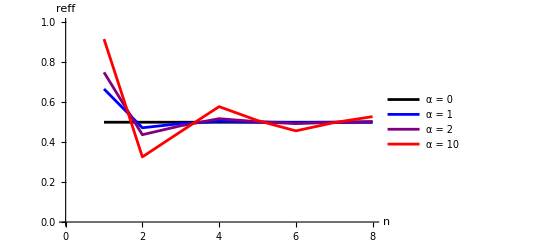

```mathematica
Show[
ListPlot[
Table[, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{"α = 0", "α = 1", "α = 2", "α = 10"},PlotRange->{Automatic,{0,1}},
AxesLabel-> {"n", "reff"}
]
]
```

### power drive

```mathematica
Clear[β]
```

we modify multiplicative drive to have a parameter β in the exponent, modifying the effect of drive:

```mathematica
wαPower[y_]:= (1+α)^(β y)/Sum[((1 + α)^(β y))[[k]], {k, 1, 4}] * Mod[y, 2]
```

and then we define a function that sums the application of this function across all chromatids:

```mathematica
q[y_]:= wαPower[y] // Total
```

is a random variable representing the proportion of recovered chromatids that are recombinant:

```mathematica
mPow = q[{x1, x2, x3, x4}]
```

((1+α)^((n-x1) β) Mod[n-x1,2])/((1+α)^((n-x1) β)+(1+α)^(x1 β)+(1+α)^((n-x3) β)+(1+α)^(x3 β))+((1+α)^(x1 β) Mod[x1,2])/((1+α)^((n-x1) β)+(1+α)^(x1 β)+(1+α)^((n-x3) β)+(1+α)^(x3 β))+((1+α)^((n-x3) β) Mod[n-x3,2])/((1+α)^((n-x1) β)+(1+α)^(x1 β)+(1+α)^((n-x3) β)+(1+α)^(x3 β))+((1+α)^(x3 β) Mod[x3,2])/((1+α)^((n-x1) β)+(1+α)^(x1 β)+(1+α)^((n-x3) β)+(1+α)^(x3 β))

finding r_eff:

```mathematica
reffPow[numcos_]:=Expectation[mPow /. n->numcos, {x1, x3} \[Distributed] pxall /. n->numcos]
```

for n = 1:

```mathematica
reffPow[1]
```

(1+α)^β/(1+(1+α)^β)

```mathematica
Table[reffPow[n], {n, 1,8}]//Simplify
```

{(1+α)^β/(1+(1+α)^β),1/4+(1+α)^β/((1+(1+α)^β)^2),(9-3 (1+α)^β+3 (1+α)^(2 β)+7 (1+α)^(3 β))/(16+16 (1+α)^(3 β)),(5+6 (1+α)^(2 β)+5 (1+α)^(4 β))/(8 (1+(1+α)^β+(1+α)^(3 β)+(1+α)^(4 β))),1/256 (100/(1+(1+α)^β)+(110 (1+α)^β)/(1+(1+α)^β)+25/(1+(1+α)^(3 β))+(20 (1+α)^(3 β))/(1+(1+α)^(3 β))+(1+α)^(5 β)/(1+(1+α)^(5 β))),1/256 (64+(150 (1+α)^β)/((1+(1+α)^β)^2)+(10 (1+α)^(3 β))/((1+(1+α)^(3 β))^2)+(45 (1+(1+α)^(4 β)))/(1+(1+α)^β+(1+α)^(3 β)+(1+α)^(4 β))+(3 (1+α)^β (1+(1+α)^(4 β)))/(1+(1+α)^β+(1+α)^(5 β)+(1+α)^(6 β))),(1519/(1+(1+α)^β)+(1484 (1+α)^β)/(1+(1+α)^β)+490/(1+(1+α)^(3 β))+(511 (1+α)^(3 β))/(1+(1+α)^(3 β))+49/(1+(1+α)^(5 β))+(42 (1+α)^(5 β))/(1+(1+α)^(5 β))+(1+α)^(7 β)/(1+(1+α)^(7 β)))/4096,1/1024(256+(245 (1+(1+α)^(2 β)))/((1+(1+α)^β)^2)+(196 (1+α)^β (1+(1+α)^(2 β)))/(1+(1+α)^β+(1+α)^(3 β)+(1+α)^(4 β))+(35 (1+(1+α)^(6 β)))/((1+(1+α)^(3 β))^2)+(28 (1+(1+α)^(6 β)))/(1+(1+α)^β+(1+α)^(5 β)+(1+α)^(6 β))+(7 (1+α)^(3 β) (1+(1+α)^(2 β)))/(1+(1+α)^(3 β)+(1+α)^(5 β)+(1+α)^(8 β))+((1+α)^β+(1+α)^(7 β))/(1+(1+α)^β+(1+α)^(7 β)+(1+α)^(8 β)))}

we plot for β = 3:

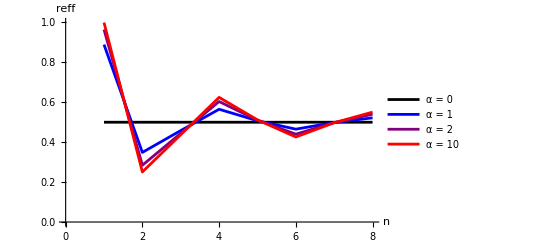

```mathematica
Show[
ListPlot[
Table[ /. β->3, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{"α = 0", "α = 1", "α = 2", "α = 10"},PlotRange->{Automatic,{0,1}},
AxesLabel-> {"n", "reff"}
]
]
```

and plot for β = 6:

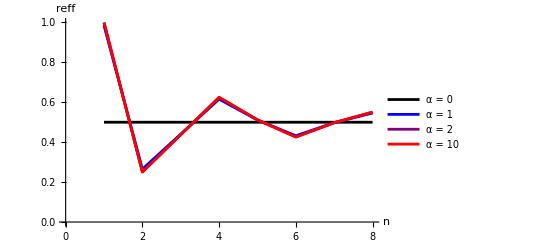

```mathematica
Show[
ListPlot[
Table[ /. β->6, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{"α = 0", "α = 1", "α = 2", "α = 10"},PlotRange->{Automatic,{0,1}},
AxesLabel-> {"n", "reff"}
]
]
```

so different β compensates for the differences in α.

### finding a general formula

we' ve defined  as the number of COs placed on the th chromatid, where , , , .

then the weighted-recombinant-state from a combination of wα functions + mod can be expressed as a random variable:
.

and then the recombinant state of the tetrad is just a sum of these:
.
and then  is just the expectation of , conditioned on :
.

then by linearity of expectation,

expanding the definition of the expectation,

we can remove the mod operation by changing the index of the inner sum, by transforming :

pulling out the factor of :

eliminating the outer sum, by symmetry:

can mathematica do this summation? first, finding a formula for :

```mathematica
Simplify[PDF[BinomialDistribution[n, 1/2], 2 * j + 1], {0 <= 2*j + 1 <= n}]
```

2^-n Binomial[n,1+2 j]

then summing:

```mathematica
4/(4 + 2*n*α)*Sum[(1 + α*(2*j + 1))*,{j, 0, Floor[n, 2]}]
```

1/(4+2 n α)(2+2 α+2^(2-n) Binomial[n,1+2 Floor[n,2]]+2^(2-n) α Binomial[n,1+2 Floor[n,2]]+(2^(1-n) n √π α Gamma[-1+n])/(Gamma[(1+n)/2] Gamma[(2+n)/2])-(3 2^-n n^2 √π α Gamma[-1+n])/(Gamma[(1+n)/2] Gamma[(2+n)/2])+(2^-n n^3 √π α Gamma[-1+n])/(Gamma[(1+n)/2] Gamma[(2+n)/2])-2^(3-n) α Binomial[n,1+2 Floor[n,2]] Floor[n,2] (-1+HypergeometricPFQ[{1,1/2-n/2+Floor[n,2],1-n/2+Floor[n,2]},{1+Floor[n,2],3/2+Floor[n,2]},1])-2^(2-n) (1+α) Binomial[n,1+2 Floor[n,2]] HypergeometricPFQ[{1,1/2-n/2+Floor[n,2],1-n/2+Floor[n,2]},{1+Floor[n,2],3/2+Floor[n,2]},1]-2^(3-n) α Binomial[n,3+2 Floor[n,2]] HypergeometricPFQ[{2,3/2-n/2+Floor[n,2],2-n/2+Floor[n,2]},{2+Floor[n,2],5/2+Floor[n,2]},1])

doesn't really work, but what if we try summing for  even and  odd separately?

for  even:

```mathematica
4/(4 + 2*n*α)*Sum[(1 + α*(2*j + 1))*,{j, 0, n/2}] // Simplify
```

1/2

for  odd:

```mathematica
additiveReffOddN[n_]:=4/(4 + 2*n*α)*Sum[(1 + α*(2*j + 1))*2^-n Binomial[n,1+2 j],{j, 0, (n-1)/2}];
additiveReffOddN[n] // Simplify
```

1/2

so we can prove that  is 1/2 for all  - in other words, additive drive has no effect.

note that the above summation doesn’t capture what we see for :

```mathematica
additiveReffOddN[1] // Simplify
```

(1+α)/(2+α)

```mathematica
(2^(1-n) n (1+α))/(2+α)
```

(2^(1-n) n (1+α))/(2+α)

```mathematica
additiveReffOddN[n_]:=4/(4 + 2*n*α)*Sum[(1 + α*(2*j + 1))*2^-n Binomial[n,1+2 j],{j, 0,(n-1)/2}]
```

```mathematica
Table[additiveReffOddN[n], {n, 0, 10}] // Simplify
```

{0,(1+α)/(2+α),1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
test[1]
```

(2 (1+α))/(4+2 α)

```mathematica
4/(4 + 2*n*α)*Sum[(1 + α*(2*j + 1))*,{j, 0, (1-1)/2}] /. n->1
```

(2 (1+α))/(4+2 α)

```mathematica
FullSimplify[%270, {n ∈ Integers, 0 <= n, 0<=α}]
```

-1/(4 (2+n α))(-4-2 n α+1/Gamma[4+2 Floor[n,2]]2^(4-n) α HypergeometricPFQ[{2,3/2-n/2+Floor[n,2],2-n/2+Floor[n,2]},{2+Floor[n,2],5/2+Floor[n,2]},1] Pochhammer[-2+n-2 Floor[n,2],3+2 Floor[n,2]]+1/Gamma[2+2 Floor[n,2]]2^(3-n) (1+α+4 α Floor[n/2]) (-1+HypergeometricPFQ[{1,1/2-n/2+Floor[n,2],1-n/2+Floor[n,2]},{1+Floor[n,2],3/2+Floor[n,2]},1]) Pochhammer[n-2 Floor[n,2],1+2 Floor[n,2]])

not really. what if we manually evaluate this at various n?

```mathematica
Table[, {n, 0, 10}]
```

Infinity::indet: Indeterminate expression 0 α ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 (1+α) ∞ encountered.

Infinity::indet: Indeterminate expression 0 α ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,-(-4-4 α)/(4 (2+2 α)),-(-4-6 α)/(4 (2+3 α)),-(-4-8 α)/(4 (2+4 α)),-(-4-10 α)/(4 (2+5 α)),-(-4-12 α)/(4 (2+6 α)),-(-4-14 α)/(4 (2+7 α)),-(-4-16 α)/(4 (2+8 α)),-(-4-18 α)/(4 (2+9 α)),-(-4-20 α)/(4 (2+10 α))}

```mathematica
Simplify[, α >= 0]
```

{Indeterminate,Indeterminate,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
Table[PDF[BinomialDistribution[q, 1/2], w],{q, 0, 10}];
```

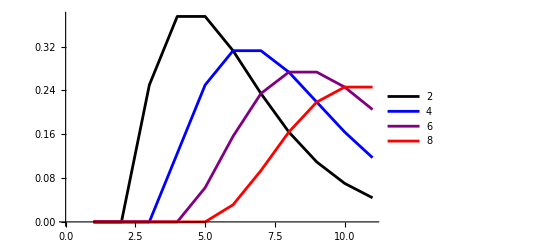

```mathematica
Show[
ListPlot[
Table[, {w, {2, 3, 4, 5}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{2, 4, 6, 8}
]
]
```

```mathematica
Table[Binomial[q, w],{q, 0, 10}]
```

{Binomial[0,w],Binomial[1,w],Binomial[2,w],Binomial[3,w],Binomial[4,w],Binomial[5,w],Binomial[6,w],Binomial[7,w],Binomial[8,w],Binomial[9,w],Binomial[10,w]}

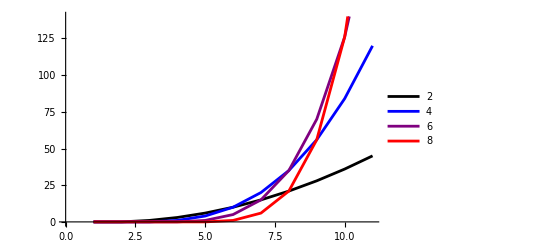

```mathematica
Show[
ListPlot[
Table[, {w, {2, 3, 4, 5}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{2, 4, 6, 8}
]
]
```

```mathematica
Simplify[PDF[BinomialDistribution[n, 1/2], 2*j],{0 <= 2*j <= n}]
```

2^-n Binomial[n,2 j]

```mathematica
Sum[Binomial[n,(2 *j + 1)], {j, 0, Floor[n, 2]}]
```

2^(-1+n)+Binomial[n,1+2 Floor[n,2]]-Binomial[n,1+2 Floor[n,2]] HypergeometricPFQ[{1,1/2-n/2+Floor[n,2],1-n/2+Floor[n,2]},{1+Floor[n,2],3/2+Floor[n,2]},1]

```mathematica
Table[ , {n, 0, 10}]
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

{Indeterminate,1,2,4,8,16,32,64,128,256,512}

```mathematica
Sum[(n!)/((2*j)!*(n-2*j)!), {j, 0, Floor[n, 2]}]
```

(n!)/((n-2 Floor[n,2])! (2 Floor[n,2])!)+(√π Gamma[n])/(Gamma[n/2] Gamma[(1+n)/2])-(n! HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1])/((n-2 Floor[n,2])! (2 Floor[n,2])!)

```mathematica
Simplify[, {n ∈ Integers, n >= 0}]
```

(n!)/((n-2 Floor[n,2])! (2 Floor[n,2])!)+(√π Gamma[n])/(Gamma[n/2] Gamma[(1+n)/2])-(n! HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1])/((n-2 Floor[n,2])! (2 Floor[n,2])!)

```mathematica
Table[, {n, 1, 10}]
```

{1,2,4,8,16,32,64,128,256,512}

```mathematica
FullSimplify[, {n ∈ Integers, n >= 0}]
```

2^(-1+n)-Binomial[n,2 Floor[n,2]] (-1+HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1])

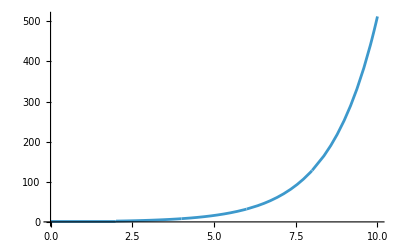

```mathematica
Plot[, {n, 0, 10}]
```

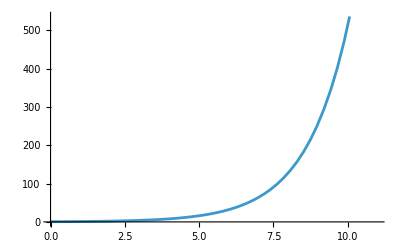

```mathematica
Plot[2^(n-1), {n, 0, 11}]
```

```mathematica
FullSimplify[ == 2^(n-1), {n ∈ Integers, n >= 0}]
```

Binomial[n,2 Floor[n,2]] (-1+HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1])==0

```mathematica
Table[, {n, 0, 20}]
```

{1/2,1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288}

```mathematica
Log[2, ] == Range[-1, 19]
```

True

```mathematica
(*Simplify[*)
Sum[(1+α*2*j)*, {j, 0, Floor[n, 2]}] /. {α -> 4}
(*]*)
```

2^(-1-n) (2^n+2 Binomial[n,2 Floor[n,2]]-(4 n √π Gamma[-1+n])/(Gamma[n/2] Gamma[(1+n)/2])+(4 n^2 √π Gamma[-1+n])/(Gamma[n/2] Gamma[(1+n)/2])-16 Binomial[n,2 Floor[n,2]] Floor[n,2] (-1+HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1])-2 Binomial[n,2 Floor[n,2]] HypergeometricPFQ[{1,-n/2+Floor[n,2],1/2-n/2+Floor[n,2]},{1/2+Floor[n,2],1+Floor[n,2]},1]-16 Binomial[n,2 (1+Floor[n,2])] HypergeometricPFQ[{2,1-n/2+Floor[n,2],3/2-n/2+Floor[n,2]},{3/2+Floor[n,2],2+Floor[n,2]},1])

```mathematica
Table[*2^-n/(4+2*n*α), {n, 2, 10}]*4
```

{5/(2 (4+4 α)),7/(4 (4+6 α)),9/(8 (4+8 α)),11/(16 (4+10 α)),13/(32 (4+12 α)),15/(64 (4+14 α)),17/(128 (4+16 α)),19/(256 (4+18 α)),21/(512 (4+20 α))}

```mathematica
Table[(1+2n)/(2^(n-1)(4+2*n*α)), {n, 2, 10}]
```

{5/(2 (4+4 α)),7/(4 (4+6 α)),9/(8 (4+8 α)),11/(16 (4+10 α)),13/(32 (4+12 α)),15/(64 (4+14 α)),17/(128 (4+16 α)),19/(256 (4+18 α)),21/(512 (4+20 α))}

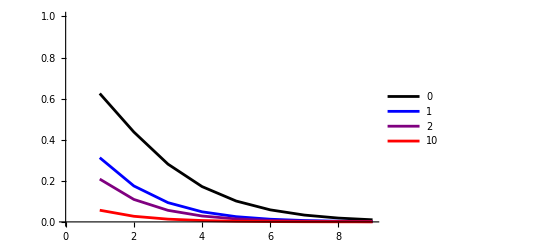

```mathematica
Show[
ListPlot[
Table[%140, {α, {0, 1, 2, 10}}],
PlotStyle->{{Black},{Blue},{Purple},{Red}},Joined->True,
PlotLegends->{0, 1, 2, 10},PlotRange->{Automatic,{0,1}}
]
]
```

```mathematica
/.α->1 // N
```

{0.3125,0.175,0.09375,0.0491071,0.0253906,0.0130208,0.00664063,0.00337358,0.00170898}

```mathematica
Table[%108 * 2^-n/(4+2*n*α),{n, 3, 11}]*4/
```

{(7 (4+4 α))/(10 (4+6 α)),(9 (4+6 α))/(14 (4+8 α)),(11 (4+8 α))/(18 (4+10 α)),(13 (4+10 α))/(22 (4+12 α)),(15 (4+12 α))/(26 (4+14 α)),(17 (4+14 α))/(30 (4+16 α)),(19 (4+16 α))/(34 (4+18 α)),(21 (4+18 α))/(38 (4+20 α)),(23 (4+20 α))/(42 (4+22 α))}

we can prove this by showing that for a random variable  , :

```mathematica
FullSimplify[
PDF[BinomialDistribution[n, 1/2], x] == PDF[BinomialDistribution[n, 1/2], n - x]
]
```

True

So then , and since this applies to x3 and x4 by symmetry, then  for all .
Then since all chromatids are identically distributed, and the drive function (wαAdd) is deterministic, drive affects all chromatids equally?
this doesn’t apply for n=1, since there are no driving nonrecombinant chromatids.

```mathematica
Binomial[n + 1, k] - Binomial[n, k]
```

-Binomial[n,k]+Binomial[1+n,k]

```mathematica
% // FullSimplify
```

-Binomial[n,k]+Binomial[1+n,k]

```mathematica
FullSimplify[
PDF[BinomialDistribution[n + 1, 1/2], x] - PDF[BinomialDistribution[n, 1/2], x],
{0 <= x <= n}
]
```

2^(-1-n) (-2 Binomial[n,x]+Binomial[1+n,x])